```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
(************** LT plot *****************************)
```

```mathematica
LTData=Import["LTplot.dat"];
temp=LTData[[All,1]];(*Temp in kelvin*);
Lum=LTData[[All,2]];(* erg s^-1*);
```

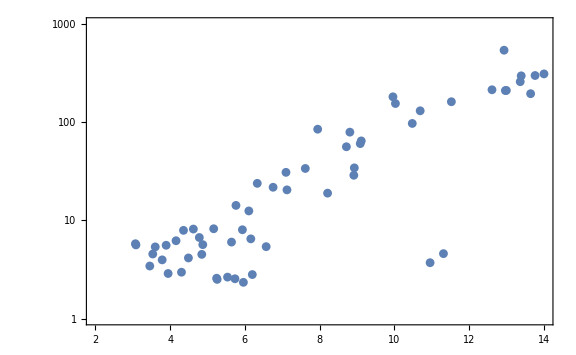

```mathematica
ListLogPlot[LTData,PlotRange->{{2,14},{1,1000}}, Frame->True,ImageSize->Large]
```

```mathematica
(********************** Mass Radius relation for WD ***************************************************)
```

```mathematica
Rsun=7 10^8(*mtr*);
Msun=2 10^30(*kg*);
Mch=1.4 Msun;
μe=2;
Rwd[M_]:=0.0126Rsun (2/μe)^(5/3)(M/Msun)^(-1/3)(1-(M/Mch)^(4/3))^(1/2)(*in mtrs*)
```

```mathematica
Rwd[0.1Msun]
```

1.87184×10^7

```mathematica
Ravg=(Rwd[0.1Msun]+Rwd[1.35Msun])/2.;
```

```mathematica
(*Calculation of Ctot *)
```

```mathematica
(************************** Definitions of Pnτ ***********************************)
Nn[R_,nn_]:=4/3 π R^3 nn
sigmaSat[R_,nn_]:=(π R^2)/Nn[R,nn]
tau[sigma_,R_,nn_]:=(3sigma)/(2sigmaSat[R,nn])
pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/(Factorial[N] tau[sigma,R,nn]^2)(Gamma[N+2]-Gamma[N+2,tau[sigma,R,nn]])
```

```mathematica
(* Numerical Values *)
vbar=20.0(*km/sec*);
vtilde=247(*km/sec*);
ηnum=√(3/(2 vbar^2))vtilde;
ρ0=10^4(*GeV/cc*);
Tsun=3 10^17; (*sec*)
fMBboosted[u_,η_,mdm_]:=ρ0/mdm(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2](*Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)*)(*x=√(3/(2 vbar^2))u*)
β[mdm_,mN_]:=(4.0mN mdm)/(mN+mdm)^2
gN[u_,vesc_,N_,mdm_,mN_]:=1/β[mdm,mN] vesc^2/(vesc^2+u^2)((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-(1/β[mdm,mN]-1);
wΩminus[σ_,u_,vesc_,N_,n_,mdm_,mN_]:=σ n (u^2+vesc^2)gN[u,vesc,N,mdm,mN]
umin[vesc_,N_,mdm_,mN_]:=vesc √((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1)-1)
umax[vesc_,N_,mdm_,mN_]:=vesc Sqrt[(1/(1-β[mdm,mN])(1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-1]
```

```mathematica
cctomtrInv=10^6;
mtrtoKm=10^-3;
```

```mathematica
CN[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,N_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mN_?NumericQ]:= π R^2 pn[σ,R,nn,N]NIntegrate[gN[u,vesc,N,mdm,mN] fMBboosted[u,ηnum,mdm]/u(u^2+vesc^2),{u,umin[vesc,N,mdm,mN],umax[vesc,N,mdm,mN]},MaxRecursion->12,WorkingPrecision->6,AccuracyGoal-> 4](cctomtrInv/ mtrtoKm)
(* UNITS : R in mtr, u in km/sec, vesc in km/sec, mdm in GeV, ρ0 in Gev/cc, σ in m^2 *)
```

```mathematica
Nmax[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mn_?NumericQ]:=For[Nobj=1,Nobj≤ 10^20,Nobj++,If[Tsun CN[R,σ,vesc,Nobj,nn,mdm,mn]≤1,Return[Nobj];Break[]]];
```

```mathematica
(*CAUTION : NEEDS to get cleared from the NSUN value before Running*)
Ctot[R_,σ_,vesc_,nn_,mdm_?NumericQ,mn_]:=Sum[CN[R,σ,vesc,n1,nn,mdm,mn],{n1,1,Nmax[R,σ,vesc,nn,mdm,mn]}]
```

```mathematica
(* Temperature of WD and asscociated constraint *)
```

```mathematica
G=6.67408×10^-11 (*m^3 kg^-1 s^-2*);
clight=3 10^8;(*m/sec*)
σ0=5.67 10^-8(*Watt m^-2 k^-4 *);
conversionfactor=6.24 10^9;(*Joule to GeV*)
```

```mathematica
RHSofConstraint[R_,T_,M_]:=4π σ0 R^2 T^4(1-(2G M)/(R clight^2))^2 conversionfactor; (* R in mtr, T in Kelvin, M in Kg *)
```

```mathematica
RHSofConstraint[0.07 10^8,4000,2 10^30]
```

5.57244×10^31

```mathematica
Ctot[0.07 10^8,10^-45,6 10^3,10^40,1.0,0.5 10^-3]
```

7.78598×10^29

```mathematica
(*Export["plotWD2.pdf",plotElecWD2];*)
```

```mathematica
MyRad=Sort[Table[r1=((Lum[[i]]624.15 10^28)/(4π conversionfactor σ0 (temp[[i]]10^3)^4))^0.5,{i,1,Length[temp]}]];(*in mtr*)
```

```mathematica
LTmytable=Table[{r1=MyRad[[i]]/10^6,lum1=Lum[[i]]624.15,Temp=temp[[i]]},{i,1,Length[temp]}];
```

```mathematica
Export["LTheatPlot.dat",LTmytable];
```

```mathematica
mdm=0.1(*GeV*);
sigma=10^-45 (*m^2*);
LDMtable=Table[{r1=MyRad[[i]]/10^6,lum2=mdm/10^28 Ctot[r1*10^6,sigma,6 10^3,10^36,mdm,0.5 10^-3]},{i,1,Length[temp]}];
```

```mathematica
sigmaSatTable=Table[{r1=MyRad[[i]]/10^6,sigmasat=sigmaSat[r1*10^6,10^36],lum3=mdm/10^28 Ctot[r1*10^6,sigmasat,6 10^3,10^36,mdm,0.5 10^-3]},{i,1,Length[temp]}];
```

```mathematica
Export["SigmaSatPlot.dat",sigmaSatTable];
```

```mathematica
Export["LDM2.dat",LDMtable];
```

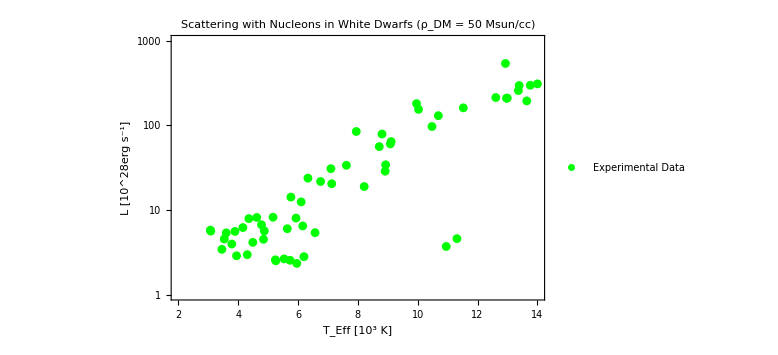

```mathematica
p2=ListLogPlot[LTData,PlotStyle->{{Thin,Green}},PlotRange->{{2,14},{1,10^3}},Frame->True,AxesOrigin ->{Automatic,Automatic},FrameLabel->{Style["T_Eff [10^3 K]",FontSize->20,Bold],Style["L [10^28erg s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"Experimental Data"},Top],PlotLabel->"Scattering with Nucleons in White Dwarfs (ρ_DM = 50 Msun/cc)"]
```

```mathematica
QualityTable=Table[{count=0.0;
LogXsec=RandomReal[{-43,-46.0}],
LogMdm=RandomReal[{-2.0,8.0}],
For[j=1,j≤ Length[temp],j++,lum2=10^LogMdm/10^28 Ctot[MyRad[[j]],10^LogXsec,6 10^3,10^36,10^LogMdm,0.5 10^-3];If[lum2≥Lum[[j]]624.15,count=count+1.0]];count/Length[temp]},{1000}];
```

```mathematica
Export["QfactorPlot.dat",QualityTable];
```